# Video Traking UI

## User Interface for gereic video tracking problems

## Step 0 - Load the program

```mathematica
Quit[];
```

```mathematica
<<VideoAnalysis`
$HistoryLength = 2; (*prevent memory overload*)
SetOptions[FFmpeg, 
"Colors"->1 (*number of color channels*),"ColorCommand"->"gray" (*indicator for "-pix_fmt" parameter:gray/rgb24*)
];
SetOptions[VideoIO,
"FrameIdFromFrame"->False
];
```

## Step 1 - Select the video file

```mathematica
VideoSelect[ "/Users/kmisiunas/Dropbox/PhD/Software/video-tracking/practice_videos/brightfield_diffusion_channel_low_density_30fps.avi"]
```

brightfield_diffusion_channel_low_density_30fps.avi has 1333 frames and is 720x480

## Step 2 - Select region of intrest

```mathematica
ROISelect[]
```

(282 | 121
460 | 150)

```mathematica
ROISelect[({{282, 121}, {460, 150}})]
```

(282 | 121
460 | 150)

## Step 3 - Compute the background image

```mathematica
VideoBufferAll[]
```

Buffer: expected 1333 frames. ffmpeg found 1333

Buffer: loaded entire video

```mathematica
bg = BackgroungUpdate[]
```

-Graphics-

## Step 4 - configure tracing algorithm

```mathematica
VideoFindThreshold[]
```

```mathematica
Options[VideoTracking];

SetOptions[VideoTracking, 
 "FilterElongation" -> {0.0, 0.5},
 "FilterArea" -> {7,50},
 "UpdateBackgroung" -> False,
 Threshold -> Automatic
]
```

{Threshold→Automatic,FilterArea→{7,50},FilterElongation→{0.,0.5},AnalysisBlockSize→4000,UpdateBackgroung→False,MinThreshold→0.05}

```mathematica
(*normal*)
SubstractBG[img_Image]:=ImageSubtract[ img, VideoTracking`Private`background]
```

```mathematica
(*for black particles*)
SubstractBG[img_Image]:=ImageDifference[img,VideoTracking`Private`background]
```

```mathematica
(*for black particles (experimental)*)
SubstractBG[img_Image]:=ImageSubtract[ 
ImageDifference[img,VideoTracking`Private`background],
ImageSubtract[ img, VideoTracking`Private`background]
]
```

## Step 5 - Inspect per frame basis (run many times!)

```mathematica
<< VideoAnalysis`
```

(451 | 65.67 | 14. | 0. | 1. | 1.76 | 2.97 | 0.28
451 | 88. | 13.61 | 0. | 1. | 1.64 | 2.96 | 0.05)

-Graphics-

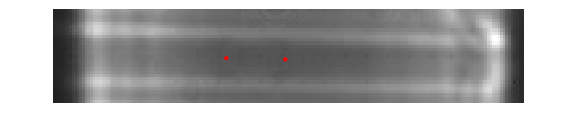

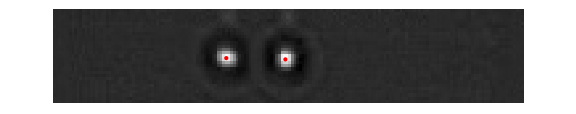

-Graphics-

Area→{1→24.375,2→23.5}

Elongation→{1→0.451369,2→0.0198308}

```mathematica
frame =451;
If[0>frame||frame >  VideoLength[], frame = 1; Print@"Frame out of range. set to 1."];

ShowTrackOverlayed[img_,list_]:=Show[img,Graphics@Flatten@{Red,Point[#]&/@list[[;;,{2,3}]]},ImageSize->Large]

curPos = VideoAnalyseFrame[frame]

ShowTrackOverlayed[ VideoGet[frame] , curPos]
ShowTrackOverlayed[ BackgroundCurrent[], curPos]
ShowTrackOverlayed[ SubstractBG@VideoGet[frame] // ImageAdjust, curPos] 
ShowTrackOverlayed[ FrameBinarize@SubstractBG@VideoGet[frame] , curPos]

"Area"-> ComponentMeasurements[ FrameBinarize@SubstractBG@VideoGet[frame] ,"Area"]

"Elongation"-> ComponentMeasurements[ FrameBinarize@SubstractBG@VideoGet[frame] ,"Elongation"]
```

## Analyse many videos

```mathematica
ComputeVideo[file_] := Module[{loadTime, analysisTime,oldROI,outputFolder},
Clear[output];
Print@"==============================================";
oldROI = ROICurrent[] ; (*reuse ROI*)

Print @VideoSelect[ file ];

Print["Video lenght (30fps eqv.): "<> ToString@(VideoLength[] /30 // N) <> " sec"];
Print ["ROI: "<> ToString@ROISelect[ oldROI ]];

loadTime = AbsoluteTiming[
VideoBufferAll[];
Print @ BackgroungUpdate[] ;
(*Print @ ImageAdjust@ImageDifference[UpdateBackgroung[bg ],GetFrame[1]];*)
][[1]];

{analysisTime,output} = AbsoluteTiming @ VideoAnalyse[];

Print[ "Analysis took (load + recognition): "<> ToString@loadTime <> " + "<> ToString@analysisTime<>" = "<> ToString@(loadTime+analysisTime)<>" sec"];
Print["Particles instances found: " <> ToString@Length@output ];

(*update time and positions to absolute ones*)

cornerPos = ROICurrent[]⟦1⟧;
output⟦All,1⟧ = VideoFrameID /@ output⟦All,1⟧ ; (*time*)
output⟦All,2⟧ += cornerPos⟦1⟧; (*x*)
output⟦All,3⟧ += cornerPos⟦2⟧; (*y*)

outputFolder = FileNameJoin[{DirectoryName[file],"raw_points"}];
If[ !FileExistsQ[outputFolder] , CreateDirectory[outputFolder ]];

Print["Done: "<>
ToString@Export[ FileNameJoin[{outputFolder, (FileBaseName[file] <>".csv")}],  output]];
]
```

#### Find files

```mathematica
analyseTheseFiles = FileNames["low_conc_square_wave_(starts_+1V_on_right)2_*.avi","E:\\Experiments\\Antony\\2015-02-12\\",1][[1]]
```

```mathematica
analyseTheseFiles=("E:\\Experiments\\Antony\\2015-02-18\\3\\2015_02_18_square_wave_s"~~ToString@#~~".avi")&/@ {7}
```

{E:\Experiments\Antony\2015-02-18\3\2015_02_18_square_wave_s7.avi}

#### Run the analysis

```mathematica
Do[ ComputeVideo[f], {f, analyseTheseFiles }]
```

```mathematica
ComputeVideo["/Users/kmisiunas/Dropbox/PhD/Software/video-tracking/practice_videos/brightfield_diffusion_channel_low_density_30fps.avi"]
```

==============================================

brightfield_diffusion_channel_low_density_30fps.avi has 1333 frames and is 720x480

Video lenght (30fps eqv.): 44.4333 sec

ROI: {{282, 121}, {460, 150}}

Buffer: expected 1333 frames. ffmpeg found 1333

Buffer: loaded entire video

-Graphics-

Analysing: frames [1 : 1333]

Overlapping particles at frame 1135

Overlapping particles at frame 1146

Overlapping particles at frame 1147

Overlapping particles at frame 1150

Overlapping particles at frame 1157

Overlapping particles at frame 1172

Overlapping particles at frame 1173

Overlapping particles at frame 1178

Overlapping particles at frame 1180

Overlapping particles at frame 1195

Overlapping particles at frame 1222

Analysis took (load + recognition): 8.618168 + 26.704585 = 35.32275 sec

Particles instances found: 2655

Done: /Users/kmisiunas/Dropbox/PhD/Software/video-tracking/practice_videos/raw_points/brightfield_diffusion_channel_low_density_30fps.csv

#### Developing preview function

```mathematica
<<KLab`
```

```mathematica
Clear[track]
```

```mathematica
tracks = KLabImport["C:\\Users\\km558\\Dropbox\\PhD\\Projects\\Electrophoresis transport, 2014\\experiments\\antony\\2015-02-18\\3\\2015_02_18_square_wave_s7.json"]
```

KLab: Imported Track Assembly
experiment→from: /Users/kmisiunas/Dropbox/PhD/Projects/Electrophoresis transport, 2014/experiments/antony/2015-02-18/3/2015_02_18_square_wave_s7.csv
comment→
time→Mon 2 Mar 2015 20:50:53
units→{frame,px_x,px_y,px_z}
array_format→2
number→78
version→2

{0→{{2.27022×10^6,224.852,232.812},{2.27022×10^6,221.889,232.941},{2.27023×10^6,219.076,233.508},{2.27023×10^6,215.832,233.85},{2.27023×10^6,212.666,233.78},12,{2.27024×10^6,157.058,237.126},{2.27024×10^6,152.712,237.691},{2.27024×10^6,147.81,237.228},{2.27024×10^6,142.432,237.472}},76,79→{1}}
 |  |  |  |

```mathematica
FilterTrack[track_]:= Select[ track, id-50≤ #[[1]]≤ id &]

DrawTrack[track_]:= 
{RandomChoice[{Red, Blue, Green,Purple, Orange, Yellow} ] ,Opacity[0.5], Disk[ Select[track, #[[1]] == id&][[1,{2,3}]], 3], Line[track[[All, {2,3}]]]};
```

```mathematica
img = FFImport[ VideoFile[], {"Frames",9480+50+15}];
id = VideoFrameID[img];

drawSegments = Select[
FilterTrack/@(tracks[[All,2]]),
Length@#>0&];

"lead positions" -> Select[drawSegments, (Last@#)[[1]] == id&][[All,-1]]

Show[img,
Graphics[Flatten[ DrawTrack/@drawSegments, 1]],
ImageSize-> Large
]
```

lead positions→{{2.27282×10^6,145.11,238.522},{2.27282×10^6,166.607,236.223},{2.27282×10^6,206.959,234.174},{2.27282×10^6,183.554,235.149}}

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

-Graphics-

Away by X:
+2px, +2px,+1,5px, +2.5